#### Define needed operators and constants

```mathematica
l= 0.25;
rmax = 20;
z$pauli=({{1, 0}, {0, -1}}); (*sigma z*)
ρ [θρ_]=({{(Cos[θρ/2])^2, Cos[θρ/2]*Sin[θρ/2]}, {Cos[θρ/2]*Sin[θρ/2], (Sin[θρ/2])^2}}); (*Density matrix*)
I$up=1/2(({{1, 0}, {0, 1}})+1*z$pauli); (*Pi_i=Z with eigenvalue 1*)
I$down=1/2(({{1, 0}, {0, 1}})-1*z$pauli);(*Pi_i=Z with eigenvalue -1*)
A[θa_]=({{Cos[θa], Sin[θa]}, {Sin[θa], -Cos[θa]}});
F[θf_]=({{Cos[θf], Sin[θf]}, {Sin[θf], -Cos[θf]}});
(*changed value in arg from 4 to 2;*)
M$A$r[r_,θa_]:=√l*(δt/(2π*τ))^(1/4)*MatrixExp[-δt/(4*τ) (MatrixPower[r({{1, 0}, {0, 1}})-A[θa],2])]/.{δt-> 0.1, τ-> 1};
M$A$r$dag[r_,θa_]:=√l*(δt/(2π*τ))^(1/4)*MatrixExp[-δt/(4*τ) (MatrixPower[r({{1, 0}, {0, 1}})-A[θa],2])]/.{δt-> 0.1, τ-> 1};
F$up[θf_]=1/2(({{1, 0}, {0, 1}})+F[θf]); (*Pi_F with eigenvalue 1*)
F$down[θf_]=1/2(({{1, 0}, {0, 1}})-F[θf]);(*Pi_F with eigenvalue -1*)
```

```mathematica
Checking properties of Kraus Operator
```

```mathematica
Sum[(M$A$r[r,0.5Pi].M$A$r$dag[r,0.5 Pi]), {r,-rmax,rmax,l}]//MatrixForm
```

(1. | -3.46945×10^-18
-7.37257×10^-18 | 1.)

Now define probabilities and entropy definitions

```mathematica
p$af$up[r_,θρ_,θa_,θf_] =Tr[F$up[θf].M$A$r[r,θa].ρ[θρ].M$A$r$dag[r,θa]];
p$af$down[r_,θρ_,θa_,θf_] = Tr[F$down[θf].M$A$r[r,θa].ρ[θρ].M$A$r$dag[r,θa]];
p$i$up[θρ_] = Tr[I$up.ρ[θρ]];
p$i$down[θρ_] = Tr[I$down.ρ[θρ]];
```

```mathematica
H$I[θρ_]=-p$i$up[θρ] Log[2,p$i$up[θρ]] -p$i$down[θρ] Log[2,p$i$down[θρ]];
H$AF$singleR [r_,θρ_,θa_,θf_] =-p$af$up[r,θρ,θa,θf]Log[2,p$af$up[r,θρ,θa,θf]]   -p$af$down[r,θρ,θa,θf]Log[2,p$af$down[r,θρ,θa,θf]];
H$AF[θρ_,θa_,θf_] = (Sum[H$AF$singleR[r,θρ,θa,θf],
{r,-rmax+(l/2),rmax-(l/2),l}]);
LHS[θρ_,θa_,θf_]  = H$I[θρ] + H$AF[θρ,θa,θf];
```

#### Export some data to compare to Igor

```mathematica
(* THIS TAKES ~30 seconds*)
lhs$numeric$ta$pi0p5 = Table[LHS[i  Pi, 0.5Pi,j  Pi], {i,0.01,0.99,0.03},{j,0.01,0.99,0.03}];
(* END LONG BLOCK *)
```

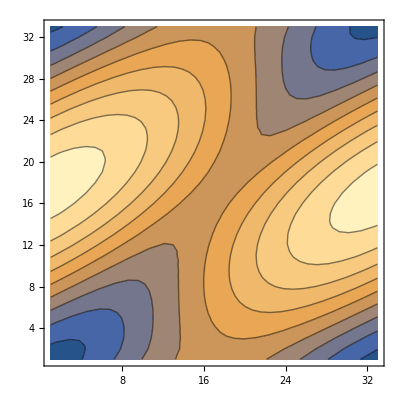

```mathematica
ListContourPlot[lhs$numeric$ta$pi0p5]
```

Investigate the theta_rho dependence of the LHS.

```mathematica
Plot3D[Re[LHS[rho Pi, 0.25Pi, f Pi]], {rho,0,1},{f,0,1}]//Timing
```

{486.346,-Graphics3D-}

```mathematica
tRho=  Pi/2;
ta= Pi/4;
tf= Pi/2;
```

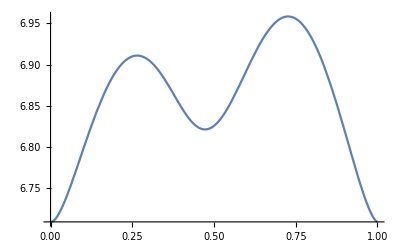
{93.7122,-Graphics-}

```mathematica
Plot[LHS[x Pi, ta, tf], {x,0,1}]//Timing
```

```mathematica
Plot[LHS[x Pi, ta, tf], {x,0,1}]//Timing
```

{115.783,-Graphics-}

```mathematica
Minimize[{LHS[x Pi, ta, tf],0≤x≤ 1},x]
Maximize[{LHS[x Pi, ta, tf],0≤x≤ 1},x]
```

{6.70842,{x→0.00157685}}

{6.95848,{x→0.726716}}

```mathematica
6.958476835220518- 6.708423268059185
```

0.250054

```mathematica
Minimize[LHS[rho Pi, aa Pi, ff Pi],{rho,aa,ff}]
```

{5.70806,{rho→-1.,aa→1.,ff→1.}}

```mathematica
Minimize[{LHS[rho Pi, aa Pi,  Pi/2]},{rho,aa}][[2]]
```

6.70806

Other calculations

```mathematica
paf$down = Table[p$af$down[i,tRho ,ta,tf ], {i,-20,20,l}];
paf$up = Table[p$af$up[i,tRho ,ta,tf ], {i,-20,20,l}];paf$down[[81]] = paf$down[[82]];
paf$up[[81]] = paf$up[[82]];
Export["paf_down.txt",paf$down];
Export["paf_up.txt",paf$up];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression (0. ComplexInfinity)/(√2) encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression (0. ComplexInfinity)/(√2) encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0. ComplexInfinity)/(√2) encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression (0. ComplexInfinity)/(√2) encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression (0. ComplexInfinity)/(√2) encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0. ComplexInfinity)/(√2) encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

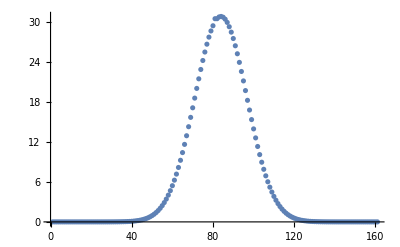

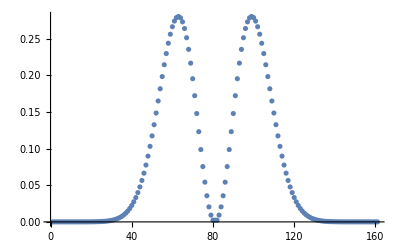

```mathematica
ListPlot[1000*paf$up]
ListPlot[1000*paf$down]
```

```mathematica
{Total[paf$down]+ Total[paf$up]}
```

{1.00044}

```mathematica
Plot3D[p$af$up[rr,rho*Pi ,ta,tf ],{rr,-20,20},{rho,0,1},PlotRange-> {0,0.04}]
```

-Graphics3D-

```mathematica
Plot3D[p$af$down[rr,rho*Pi ,ta,tf ],{rr,-20,20},{rho,0,1},PlotRange-> Full]
```

-Graphics3D-

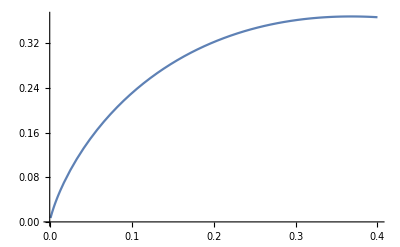

```mathematica
Plot[-x Log[x], {x,0.001, 0.4}]
```